# Convergent beam crystallography project

```mathematica
w0=10^-5;
λ=1.5 10^-7;
a=2 10^-5;
b=2.5 10^-5;
c=3 10^-5;
Nx=20;
Ny=20;
Nz=4;
```

```mathematica
k[λ_]:=2π/λ
θdiv[w0_,λ_]:=λ/(π w0)
zR[w0_,λ_]:=k[λ]w0^2/2
wz[z_,w0_,λ_]:=w0(1+(z/zR[w0,λ])^2)^(1/2)
u[x_,y_,z_,w0_,λ_]:=1/(π w0^2)Exp[ⅈ k[λ]z]/(1+2ⅈ z/(k[λ] w0^2))Exp[-(x^2+y^2)/(w0^2(1+2ⅈ z/(k[λ] w0^2)))]
uf[kx_,ky_,z_,w0_,λ_]:=1/(4 π^2)Exp[-(kx^2+ky^2)k[λ]^2(w0^2/4+(ⅈ z)/(2k[λ]))]Exp[ⅈ k[λ]z]
```

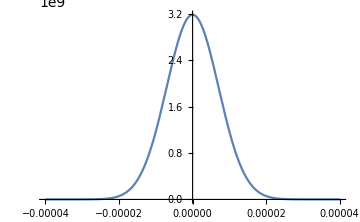
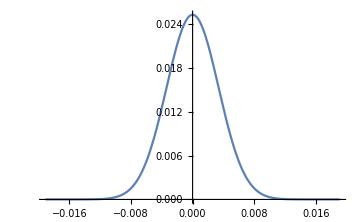

```mathematica
Row[{Plot[Abs[u[x,0,0,w0,λ]],{x,-4w0,4w0},PlotRange->{Full,{0,1/(π w0^2)}},ImageSize->Medium],Plot[Abs[uf[kx,0,0,w0,λ]],{kx,-4θdiv[w0,λ],4θdiv[w0,λ]},PlotRange->{Full,{0,1/(4 π^2)}},ImageSize->Medium]}]
```

```mathematica
asfcoeffsAu={1.67773900 10^1,1.93171560 10^1,3.29796830 10^1,5.59545300,1.05768540 10^1,-1.03848619 10^1,1.22737000 10^-1,8.62157000 ,1.25690200,3.80088200 10^1,6.01000000 10^-4};
acoeffs=asfcoeffsAu[[;;5]];
bcoeffs=asfcoeffsAu[[7;;]];
ccoeff=asfcoeffsAu[[6]];
ASF[s_,acoeffs_,bcoeffs_,c_]:=Total[MapThread[#1*Exp[-#2 s^2]&,{acoeffs,bcoeffs}]]+c
```

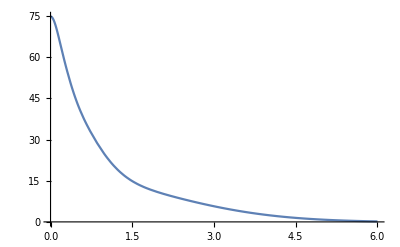

```mathematica
Plot[ASF[s,acoeffs,bcoeffs,ccoeff],{s,0,6}]
```

```mathematica
Lattice[a_,b_,c_,Nx_,Ny_,Nz_,orig_:{0,0,0}]:=Flatten[Table[{a i+orig[[1]],a j+orig[[2]],a k+orig[[3]]},{i,(-Nx+1)/2.,(Nx-1)/2.},{j,(-Ny+1)/2.,(Ny-1)/2.},{k,(-Ny+1)/2.,(Ny-1)/2.}],2]
```

```mathematica
us=Quiet[Map[u[#1,#2,#3,w0,λ]&@@#&,Lattice[a,b,c,Nx,Ny,Nz]]];
```

## Convolution prototyping

```mathematica
PSDNorm[x_,μ_,σ_]:=1/(√π σ)Exp[-(x-μ)^2/σ^2]
```

```mathematica
NIntegrate[PSDNorm[x,0,1]^2,{x,-4,4}]
NIntegrate[uf[kx,ky,0,w0,λ]^2,{kx,-4θdiv[w0,λ],4θdiv[w0,λ]},{ky,-4θdiv[w0,λ],4θdiv[w0,λ]}]
```

0.398942

2.29765×10^-8

```mathematica
udist[kx_,ky_,w0_,λ_]:=PDF[BinormalDistribution[{0,0},{θdiv[w0,λ]/√2,θdiv[w0,λ]/√2},0],{kx,ky}]
```

```mathematica
NIntegrate[√(kx^2+ky^2)udist[kx,ky,w0,λ],{kx,-8θdiv[w0,λ],8θdiv[w0,λ]},{ky,-8θdiv[w0,λ],8θdiv[w0,λ]}]2/√π
θdiv[w0,λ]
NIntegrate[(4 π^2)/(π θdiv[w0,λ]^2)√(kx^2+ky^2)uf[kx,ky,0,w0,λ],{kx,-4θdiv[w0,λ],4θdiv[w0,λ]},{ky,-4θdiv[w0,λ],4θdiv[w0,λ]}]
```

0.00477465

0.00477465

0.00423142

## Bessel beam

```mathematica
besself[kx_,ky_,z_,w0_,λ_]:=1/π(λ/(π w0))^-2 UnitStep[λ/(π w0)-√(kx^2+ky^2)]Exp[ⅈ (2π)/λ z(1-(kx^2+ky^2)/2)]
besself2[θ_,z_,w0_,λ_]:=UnitStep[λ/(π w0)-θ]Exp[ⅈ (2π)/λ z(1-θ^2/2)]
bessel[x_,y_,w0_,λ_]:=1/(π θdiv[w0,λ])BesselJ[1,k[λ]θdiv[w0,λ] √(x^2+y^2)]/(√(x^2+y^2))
```

## Lens beam

```mathematica
RBeamIntegrand[x_,xx_,y_,yy_,z_,f_,λ_]:=-(ⅈ Exp[ⅈ k[λ]z])/(λ z)Exp[(ⅈ k[λ])/(2z)(x^2+y^2)]Exp[-(ⅈ k[λ])/2(xx^2+yy^2)(1/f-1/z)]Exp[-(ⅈ k[λ])/z(x xx+y yy)]
RBeam[x_,y_,z_,a_,f_,λ_]:=NIntegrate[RBeamIntegrand[x,xx,y,yy,z,f,λ],{xx,-a,a},{yy,-a,a}]
```

```mathematica
CBeamIntegrand[r_,rr_,z_,f_,λ_]:= -(ⅈ Exp[ⅈ k[λ]z])/(λ z)Exp[(ⅈ k[λ])/(2z)r^2]Exp[-(ⅈ k[λ])/2 rr^2(1/f-1/z)]BesselJ[0,k[λ]r rr/z]
CBeam[r_,z_,a_,f_,λ_]:=NIntegrate[2π rr CBeamIntegrand[r,rr,z,f,λ],{rr,0,a}]
```

```mathematica
DxRBeamIntegrand[x_,xx_,z_,f_,λ_]:=(x-xx)Exp[-(ⅈ k[λ])/2(xx^2)(1/f-1/z)]Exp[-(ⅈ k[λ])/z x xx]
```

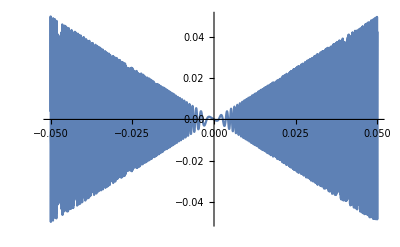

```mathematica
f=2.0;
ap=5 10^-2;
δz=10^-5;
Plot[Re[DxRBeamIntegrand[a,x,f+0.1,f,λ]],{x,-ap,ap}]
```